# Discontinuous Galerkin

## Weak Formulation (Modal DG)

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Legendre Polynomials

```mathematica
legendreP =Table[LegendreP[i,𝒳],{i,0,6}];
Column[legendreP] // TraditionalForm
```

1
𝒳
1/2 (3 𝒳^2-1)
1/2 (5 𝒳^3-3 𝒳)
1/8 (35 𝒳^4-30 𝒳^2+3)
1/8 (63 𝒳^5-70 𝒳^3+15 𝒳)
1/16 (231 𝒳^6-315 𝒳^4+105 𝒳^2-5)

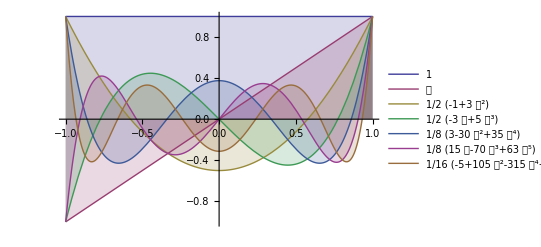

```mathematica
Plot[Evaluate[legendreP],{𝒳,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## Scaled Orthogonal Polynomials

Define the size of our interval, I_j, as Δx_j. This interval and it will be identified by its middel point x_j. Notice that our basis polynomials work on the range of [-1,1]. Thus we are now interested in finding a way to scale them to and dimensionless interval I_j with range [-1/2,1/2].

The first idea to scale them is by making the change of variable 𝒳 → (x-x_j)/Δx_j, and using grand Schmidt ortogonalization process to build a new set or orthogonal polynomials.

### Initialize Notation

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-1/2,1/2}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

∫_(-1/2)^(1/2) v_1[z]^2 ⅆz

```mathematica
<a z,z>
```

a/12

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

### Building Scaled Legendre Polynomials using Gram Schmidt Orthogonalization process

#### Procedure 1: (not so good...)

based on http : // en.wikipedia.org/wiki/Gram - Schmidt_process, we configure :

Defining our initial vectors,

```mathematica
Table[Subscript[v, i]=z^i,{i,0,6}](* here z = x-Subscript[x, j] *)
```

{1,z,z^2,z^3,z^4,z^5,z^6}

Compute initial projection

```mathematica
Subscript[u, 0]=Subscript[v, 0]
```

1

```mathematica
Subscript[u, 1]=Subscript[v, 1]-Subscript[proj, Subscript[u, 0]][Subscript[v, 1]]
```

z

```mathematica
scaledLegendre = Table[Subscript[u, i+1]=Subscript[v, i+1]-Subscript[proj, Subscript[u, i-1]][Subscript[v, i+1]] -Subscript[proj, Subscript[u, i]][Subscript[v, i+1]],{i,1,5}] ;
```

```mathematica
scaledLegendre /. z -> (x-Subscript[x, j])/Subscript[Δx, j]//Simplify// Column
```

-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
-3/14 (-1/12+(x-x_j)^2/Δx_j^2)+(x-x_j)^4/Δx_j^4
-5/18 ((x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j))+(x-x_j)^5/Δx_j^5
-(885 (-3/14 (-1/12+(x-x_j)^2/Δx_j^2)+(x-x_j)^4/Δx_j^4))/4444+(x-x_j)^6/Δx_j^6

#### Procedure 2: (way much better)

based on http : // mathworld.wolfram.com/Gram - SchmidtOrthonormalization.html, we configure :

```mathematica
Subscript[p, 0]=1;
Subscript[p, 1]=(z - (<z Subscript[p, 0],Subscript[p, 0]>)/(<Subscript[p, 0],Subscript[p, 0]>))Subscript[p, 0];
```

```mathematica
scaledLegendre=Table[Subscript[p, i+1]=(z - (<z Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i],Subscript[p, i]>))Subscript[p, i] -(<Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i-1],Subscript[p, i-1]>)Subscript[p, i-1] ,{i,1,6}]//Expand ;
```

```mathematica
scaledLegendre = Join[{Subscript[p, 0],Subscript[p, 1]},scaledLegendre];
```

```mathematica
scaledLegendre //Column
```

1
z
-1/12+z^2
-(3 z)/20+z^3
3/560-(3 z^2)/14+z^4
(5 z)/336-(5 z^3)/18+z^5
-5/14784+(5 z^2)/176-(15 z^4)/44+z^6
-(35 z)/27456+(105 z^3)/2288-(21 z^5)/52+z^7

How about using rewritting in the form z = (x-x_j)/Δx_j. we have,

```mathematica
scaledLegendre /.z->(x-Subscript[x, j])/Subscript[Δx, j]//Column
```

1
(x-x_j)/Δx_j
-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
3/560+(x-x_j)^4/Δx_j^4-(3 (x-x_j)^2)/(14 Δx_j^2)
(x-x_j)^5/Δx_j^5-(5 (x-x_j)^3)/(18 Δx_j^3)+(5 (x-x_j))/(336 Δx_j)
-5/14784+(x-x_j)^6/Δx_j^6-(15 (x-x_j)^4)/(44 Δx_j^4)+(5 (x-x_j)^2)/(176 Δx_j^2)
(x-x_j)^7/Δx_j^7-(21 (x-x_j)^5)/(52 Δx_j^5)+(105 (x-x_j)^3)/(2288 Δx_j^3)-(35 (x-x_j))/(27456 Δx_j)

which is in total agreement with the polynomials used in “RKDG for conservation laws II”, paper of 1989.
Now observe their orthogonality behavior,

```mathematica
Table[(<scaledLegendre[[i]],scaledLegendre[[j]]>),{i,1,7},{j,1,7}] //TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/180 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2800 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/44100 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/698544 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/11099088

we observe that they are indeed orthogonal but not orthonormal. We then need to define normalization contatns

```mathematica
ClearAll[a]
```

```mathematica
Diagonal[Table[Subscript[a, n,m]=(<Subscript[p, n],Subscript[p, m]>),{n,0,6},{m,0,6}]]
```

{1,1/12,1/180,1/2800,1/44100,1/698544,1/11099088}

Make a double check

```mathematica
Table[1/Subscript[a, n,n](<Subscript[p, n],Subscript[p, n]>),{n,0,6}]
```

{1,1,1,1,1,1,1}

Now in this form we have scaled orthogonal polynomials! ; )

#### Procedure 3: (the mathematica way)

```mathematica
scaledLegendre3 = Orthogonalize[{1,z,z^2,z^3,z^4,z^5,z^6},Integrate[#1 #2,{z,-1/2,1/2}]&] //Expand;
```

```mathematica
scaledLegendre3 //Column
```

1
2 √3 z
-(√5)/2+6 √5 z^2
-3 √7 z+20 √7 z^3
9/8-45 z^2+210 z^4
(15 √11 z)/4-70 √11 z^3+252 √11 z^5
-(5 √13)/16+(105 √13 z^2)/4-315 √13 z^4+924 √13 z^6

Observe their Orthogonality behavior,

```mathematica
Table[(<scaledLegendre3[[i]],scaledLegendre3[[j]]>),{i,1,7},{j,1,7}] //TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1

These are already orthonormal polynomials!

### Plot Scaled Legendre Polynomials

So, having this scaled functions we can think on using them as basis functions to expand otherpolynomials just as we did in classical Finite Element Methods,

First we plot the scaled polynomials that professor Cockburn and Shu are using in their publications,

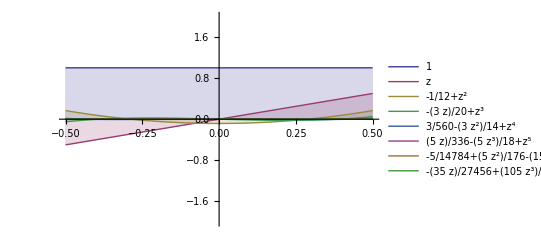

```mathematica
orthogonalpolinomials = scaledLegendre ;
Plot[Evaluate[orthogonalpolinomials],{z,-1/2,1/2},
Filling->Axis,PlotLegends->"Expressions",PlotRange->{-2,2}]
```

Comparing to the polynomials we have derived with mathematica orthogonal function,

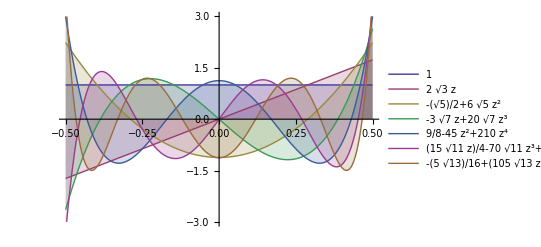

```mathematica
orthogonalpolinomials = scaledLegendre3;
Plot[Evaluate[orthogonalpolinomials],{z,-1/2,1/2},
Filling->Axis,PlotLegends->"Expressions",PlotRange->{-3,3}]
```

We can observe that their behavior is totally different for the same dimensionless intervale: I: [-1/2,1/2].

### Derivative of the scaled polynomials

```mathematica
dscaledpolynomials = D[scaledLegendre,z];
dscaledpolynomials /.z -> (x-Subscript[x, j])/Subscript[Δx, j] //Column
```

0
1
(2 (x-x_j))/Δx_j
-3/20+(3 (x-x_j)^2)/Δx_j^2
(4 (x-x_j)^3)/Δx_j^3-(3 (x-x_j))/(7 Δx_j)
5/336+(5 (x-x_j)^4)/Δx_j^4-(5 (x-x_j)^2)/(6 Δx_j^2)
(6 (x-x_j)^5)/Δx_j^5-(15 (x-x_j)^3)/(11 Δx_j^3)+(5 (x-x_j))/(88 Δx_j)
-35/27456+(7 (x-x_j)^6)/Δx_j^6-(105 (x-x_j)^4)/(52 Δx_j^4)+(315 (x-x_j)^2)/(2288 Δx_j^2)

```mathematica
Table[Subscript[dp, i]= dscaledpolynomials[[i+1]],{i,0,7}];
```

```mathematica
dcoefficients = Table[Subscript[b, n,m]= (<Subscript[p, n],Subscript[dp, m]>),{n,0,7},{m,0,7}];
dcoefficients //TableForm
```

0 | 1 | 0 | 1/10 | 0 | 1/126 | 0 | 1/1716
0 | 0 | 1/6 | 0 | 1/70 | 0 | 1/924 | 0
0 | 0 | 0 | 1/60 | 0 | 1/756 | 0 | 1/10296
0 | 0 | 0 | 0 | 1/700 | 0 | 1/9240 | 0
0 | 0 | 0 | 0 | 0 | 1/8820 | 0 | 1/120120
0 | 0 | 0 | 0 | 0 | 0 | 1/116424 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/1585584
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Discretization of I_j

### Discretization in one-dimension

Now assume that we are interested on using these polynomials in conjuction with a Legendre-Gauss-Lobatto (LGL) quadrature in our interval I_j.
We first the original 4 points gauss Lobatto quadrature info for a traditional interval of [-1,1]

```mathematica
abscissas = {-1,1/Sqrt[5],-1/Sqrt[5],1}; weights={1/6,5/6,5/6,1/6};
```

Now, we wish to scale them to fit in I_j. We mutiply our abscissas by factor Δx_j/2 or a jacobian, J, transformation term in higher dimensions, and weight would remain the same:

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}  = abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

As an example, here I’ll assume and a random interval with left and right boundaries located at [1/3,2/3]. First we proceed to create the corresponding local nodes inside the cell:

```mathematica
Subscript[x, l] = 1/3; Subscript[x, r] =2/3; Subscript[Δx, j]=Subscript[x, r]-Subscript[x, l];Subscript[x, j] = (Subscript[x, l]+Subscript[x, r])/2; {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}= Subscript[x, j]+Subscript[Δx, j]/2 abscissas
```

Set::shape: Lists {x_1, x_2, x_3, x_4} and 1/2 + abscissas/6 are not the same shape.

1/2+abscissas/6

Therefore we can perform now any integration over I_jin simple numerical way, example

```mathematica
N[∫_Subscript[x, l]^Subscript[x, r] Sin[𝓍]ⅆ𝓍 ,12]
```

0.159069685538

compare to its numerical counter part:

```mathematica
N[Subscript[Δx, j]/2∑_(i=1)^4 Subscript[w, i] Sin[Subscript[x, i]] ,12]
```

0.159069685393

### Discretization in two-dimensions and generalization

#### Quadrilateral element

Let us take advantage of the 1D case and use the same set of LGL quadrature points but in this case we will perfrom it first over a quadrilateral element with vertices located at,

```mathematica
({{Subscript[x, 1], Subscript[y, 1]}, {Subscript[x, 2], Subscript[y, 2]}, {Subscript[x, 3], Subscript[y, 3]}, {Subscript[x, 4], Subscript[y, 4]}}) = ({{-1, -1}, {-1, 1}, {1, 1}, {1, -1}});
```

#### Triangular element

## Translating from Degress of Freedom, u_j^(i)(t), to aproximate solution, u^h(x,t)

Here we are interested in understanding the expansion of these polynomials from a continuous form to a pieze wize for of the from.

### Initialization

#### Build Notation

```mathematica
Symbolize[Subscript[u, h]];Symbolize[u^_];
```

```mathematica
Subscript[u, 1]//InputForm
```

Subscript[u, 1]

```mathematica
u^(l) // InputForm
```

u⎵Superscript⎵LeftParenthesis⎵l⎵RightParenthesis

```mathematica
Table[ToExpression[RowBox[{"{",ToString[i],"}"}]],{i,10}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Notation[∫_Subscript[I, j] f_ⅆx_ ⟹ Integrate[f_,{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

#### Case1: assume the Riemann IC:

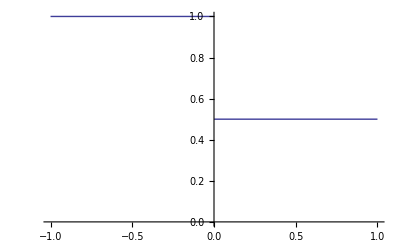

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

#### Case2: assume Sinusoidal wave function :

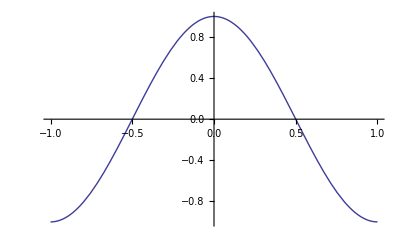

```mathematica
u[x_,t_]:= Cos[π x];
Plot[u[x,t],{x,-1,1},PlotRange->Full]
```

### Method 1: Traditional Way

#### Degrees of Freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

of course, we need to define u[x,t] in order to continue. We traditionally have two choises a continuous or a discontinuous function,

Therefore :

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} = Table[ 1/Subscript[Δx, j]^(l+1)∫_Subscript[I, j] (u[x,t] Subscript[v, l])ⅆx,{l,0,6}];
```

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} //MatrixForm
```

(0.75
-0.0625
0.
0.0015625
0.
-0.000062004
0.)

#### Solution Approximation u_h

And the approximation of the solution u(x,t) as u_h, is defined as follows

u^h[x,t] = ∑_(l=0)^k a_l u_j^(l)[t]v_l^(j)[x], for x ∈ I_j

here a_l are contants values found to normalize the contribution of each polinomial.

Following the last example we can proceed to compute from the degress of freedom the approximate solution u_h,

```mathematica
NSum[Subscript[a, l] u^(l)Subscript[v, l],{l,0,3}]
```

NSum::nsnum: Summand (or its derivative) a_l\ u^l\ v_l is not numerical at point l = 0.

NSum[a_l u^l v_l,{l,0,3}]

### Method 2: The Vandermonde Matrix

#### Degrees of Freedom u_j^(l)

From previous calculations we can do:

```mathematica
Table[Subscript[v, i]= Expand[Subscript[p, i]],{i,0,6}];(* recall that z -> (x-Subscript[x, j])/Subscript[Δx, j] *)
Table[Subscript[v, i],{i,0,6}]//MatrixForm
```

(1
z
-1/12+z^2
-(3 z)/20+z^3
3/560-(3 z^2)/14+z^4
(5 z)/336-(5 z^3)/18+z^5
-5/14784+(5 z^2)/176-(15 z^4)/44+z^6)

Evaluating every escaled polynomial for the computed abcsissas we get:

```mathematica
vandermonde = Table[Subscript[v, n]/.z->Subscript[x, m],{m,1,4},{n,0,3}];
vandermonde //MatrixForm
```

(1 | 1/3 | 1/36 | -7/540
1 | 1/2+1/(6 √5) | -1/12+(1/2+1/(6 √5))^2 | -3/20 (1/2+1/(6 √5))+(1/2+1/(6 √5))^3
1 | 1/2-1/(6 √5) | -1/12+(1/2-1/(6 √5))^2 | -3/20 (1/2-1/(6 √5))+(1/2-1/(6 √5))^3
1 | 2/3 | 13/36 | 53/270)

if for the case every we are using equally distributed cells, we can just program the numerical version of this matrix:

```mathematica
vandermonde //MatrixForm//N
```

(1. | 0.333333 | 0.0277778 | -0.012963
1. | 0.574536 | 0.246758 | 0.103469
1. | 0.425464 | 0.0976866 | 0.0131979
1. | 0.666667 | 0.361111 | 0.196296)

#### Solution Approximation u_h

## Other Math Objects

Math Objects that we are going to be dealing with

### Mass Matrix

### B Matrix

### Lift Operator

## Conservation Laws in one-dimension

### Derivation of Governing Equation

Here we consider numerical solutions of the equations of the hyperbolic conservation laws

∂_t u+∂_x f[u]=0

equipped with suitable initial or initial-boundary conditions. Let us examing the RHS:

```mathematica
D[u[x,t], t]+D[f[u[x,t]], x]
```

u^(0,1)[x,t]+f'[u[x,t]] u^(1,0)[x,t]

## Conservation Laws in Multidimension

### Derivation of Goberning Equation

Here we consider numerical solutions of the equations of the hyperbolic conservation laws

∂_t u+∑_(i=1)^d ∂_x_i f[u]=0

equipped with suitable initial or initial - boundary conditions. Let us examing the RHS :

```mathematica
D[u[x,t], t]+D[f[u[x,t]], x]
```

u^(0,1)[x,t]+f'[u[x,t]] u^(1,0)[x,t]